```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

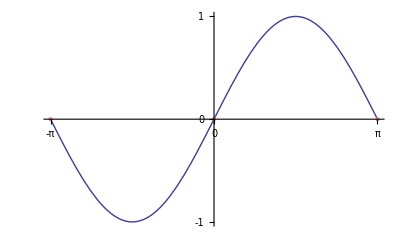
{-Graphics-,{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/discreteFourierRangeFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/discreteFourierRangeFig1pn.png}}

```mathematica
Module[{ p, g, b }, 
p = Plot[Sin[x],{x, -Pi, Pi}, Ticks -> {{-Pi, 0, Pi}, {-1, 0, 1}}] ;
g = Graphics[{PointSize[Large],Pink, Point[{#, 0} &/@ { -Pi, 0, Pi} ] 
}] ;

b = Show[p, g] ;

{b, peeters`exportForLatex["discreteFourierRangeFig1", b] }
]
```